### symbolic inversion

```mathematica
k=(kx^2+ky^2)^(1/2)
Ω=(kx^2+ky^2+I*ρ*ω/μ)^(1/2)
ux[x_,y_,z_,t_]=(Ax*Exp[Ω*z]+Bx*Exp[-Ω*z]-A/ρ*kx/ω*Exp[k*z]-B/ρ*kx/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uy[x_,y_,z_,t_]=(Ay*Exp[Ω*z]+By*Exp[-Ω*z]-A/ρ*ky/ω*Exp[k*z]-B/ρ*ky/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uz[x_,y_,z_,t_]=(Az*Exp[Ω*z]+Bz*Exp[-Ω*z]+I*A/ρ*k/ω*Exp[k*z]-I*B/ρ*k/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
P[x_,y_,z_,t_]=-ρ*g*z+(A*Exp[k*z]+B*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
h[x_,y_,z_,t_]=h0+H*Exp[I*(kx*x+ky*y+ω*t)]
subs1={A->KroneckerDelta[k1,1]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],B->KroneckerDelta[k1,2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ax->KroneckerDelta[k1,3]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bx->KroneckerDelta[k1,4]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ay->KroneckerDelta[k1,5]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],By->KroneckerDelta[k1,6]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Az->KroneckerDelta[k1,7]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bz->KroneckerDelta[k1,8]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2], H->KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2]};
subs2={kx->qx+n1*q1.{1,0}+m1*q2.{1,0},ky->qy+n1*q1.{0,1}+m1*q2.{0,1},ω->ω+l1*ωd};
```

√(kx^2+ky^2)

√(kx^2+ky^2+(ⅈ ρ ω)/μ)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bx ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ax ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) kx)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) kx)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (By ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ay ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) ky)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) ky)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bz ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Az ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(ⅈ B ⅇ^(-√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω)+(ⅈ A ⅇ^(√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (B ⅇ^(-√(kx^2+ky^2) z)+A ⅇ^(√(kx^2+ky^2) z))-g z ρ

ⅇ^(ⅈ (kx x+ky y+t ω)) H+h0

```mathematica
Expand[D[ux[x,y,z,t],t]-μ/ρ*(D[ux[x,y,z,t],{x,2}]+D[ux[x,y,z,t],{y,2}]+D[ux[x,y,z,t],{z,2}])+D[P[x,y,z,t],x]/ρ]
Expand[D[uy[x,y,z,t],t]-μ/ρ*(D[uy[x,y,z,t],{x,2}]+D[uy[x,y,z,t],{y,2}]+D[uy[x,y,z,t],{z,2}])+D[P[x,y,z,t],y]/ρ]
Expand[D[uz[x,y,z,t],t]-μ/ρ*(D[uz[x,y,z,t],{x,2}]+D[uz[x,y,z,t],{y,2}]+D[uz[x,y,z,t],{z,2}])+D[P[x,y,z,t],z]/ρ+g]
```

0

0

0

```mathematica
eqs1=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs1/.subs2],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs1/.subs2],(I*kx*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[ux[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,(I*ky*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[uy[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Expand[(-ρ*g*(h[x,y,z,t]-h0)+(P[x,y,h0,t]+ρ*g*h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,3]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,4]*I2m[l1,m1,m2,n1,n2])-kx/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]+KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,5]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,6]*I2m[l1,m1,m2,n1,n2])-ky/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]+KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,7]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,8]*I2m[l1,m1,m2,n1,n2])+I*k/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]-KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2]},{k1,1,9}]];
```

```mathematica
elim=Range[6];
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[8],Length[elim]],u_/;Length[u]==Length[elim]]];
Monitor[dets=Table[Expand[Det[eqs1[[elim,perts[[i]]]]]],{i,1,Length[perts]}];,i]
lperts=DeleteDuplicates[First/@Position[dets,u_/;Abs[u]≠0.]]
ipert=lperts[[7]]
First/@subs1[[Complement[Range[9],perts[[ipert]]]]]
```

{2,3,4,5,7,8,9,10,11,12,13,14,18,19,20,21,24,25,26,27}

9

{Bx,By,H}

```mathematica
mat=FullSimplify[Expand[FullSimplify[Simplify[eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]/.m2->m1/.n2->n1/.l2->l1].(eqs1[[elim,Complement[Range[9],perts[[ipert]]]]]/.m2->m1/.n2->n1/.l2->l1)/.qx->(κx-n1 q1.{1,0}-m1 q2.{1,0})/.qy->(κy-n1 q1.{0,1}-m1 q2.{0,1})/.ω->-I*μ/ρ(ρ/μ*Ω1[n1,m1,l1]-κx^2-κy^2)-l1 ωd/.κx^2->κ1[n1,m1]^2-κy^2,κ1[n1,m1]>0&&Ω1[n1,m1,l1]>0]/.κx^2->κ1[n1,m1]^2-κy^2/.κx->κx[n1,m1]/.κy->κy[n1,m1]/.l2->l1].DiagonalMatrix[{ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ)),ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ)),ρ}]]/.I2m[l1,m1,m2,n1,n2]->(C2[l1,m1,m2,n1,n2]+S2[l1,m1,m2,n1,n2])/2/ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))/.I2p[l1,m1,m2,n1,n2]->(C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2])/2/ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))/.I1m[m1,m2,n1,n2]->(C1[m1,m2,n1,n2]+S1[m1,m2,n1,n2])/2/ⅇ^(h0 κ1[n1,m1])/.I1p[m1,m2,n1,n2]->(C1[m1,m2,n1,n2]-S1[m1,m2,n1,n2])/2/ⅇ^(-h0 κ1[n1,m1])]/.-κ1[n1,m1]^2+κy[n1,m1]^2->-κx[n1,m2]^2;
MatrixForm[Total/@FullSimplify[CoefficientRules[#,{C1[m1,m2,n1,n2],C2[l1,m1,m2,n1,n2],S1[m1,m2,n1,n2],S2[l1,m1,m2,n1,n2]}]]&/@mat/.Rule[a_,b_]:>b*C1[m1,m2,n1,n2]^a[[1]]*C2[l1,m1,m2,n1,n2]^a[[2]]*S1[m1,m2,n1,n2]^a[[3]]*S2[l1,m1,m2,n1,n2]^a[[4]]]
```

(C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κx[n1,m2]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -ⅈ μ √(ρ/μ) C2[l1,m1,m2,n1,n2] κx[n1,m1] √Ω1[n1,m1,l1]+ⅈ μ √(ρ/μ) S2[l1,m1,m2,n1,n2] κx[n1,m1] √Ω1[n1,m1,l1]-(ⅈ C1[m1,m2,n1,n2] κx[n1,m1] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1])))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))-(ⅈ S1[m1,m2,n1,n2] κx[n1,m1] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))/(2 κ1[n1,m1])
-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κy[n1,m1]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -ⅈ μ √(ρ/μ) C2[l1,m1,m2,n1,n2] κy[n1,m1] √Ω1[n1,m1,l1]+ⅈ μ √(ρ/μ) S2[l1,m1,m2,n1,n2] κy[n1,m1] √Ω1[n1,m1,l1]-(ⅈ C1[m1,m2,n1,n2] κy[n1,m1] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1])))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))-(ⅈ S1[m1,m2,n1,n2] κy[n1,m1] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))/(2 κ1[n1,m1])
(ⅈ S2[l1,m1,m2,n1,n2] κx[n1,m1])/(√((ρ Ω1[n1,m1,l1])/μ))-(2 ⅈ μ S1[m1,m2,n1,n2] κ1[n1,m1] κx[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | (ⅈ S2[l1,m1,m2,n1,n2] κy[n1,m1])/(√((ρ Ω1[n1,m1,l1])/μ))-(2 ⅈ μ S1[m1,m2,n1,n2] κ1[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -μ C2[l1,m1,m2,n1,n2] κ1[n1,m1]^2+μ S2[l1,m1,m2,n1,n2] κ1[n1,m1]^2+1/2 C1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])+(S1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √((ρ Ω1[n1,m1,l1])/μ))))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])))

```mathematica
FullSimplify[MatrixForm[Total/@FullSimplify[CoefficientRules[#,{C1[m1,m2,n1,n2],C2[l1,m1,m2,n1,n2],S1[m1,m2,n1,n2],S2[l1,m1,m2,n1,n2]}]]&/@mat/.Rule[a_,b_]:>b*C1[m1,m2,n1,n2]^a[[1]]*C2[l1,m1,m2,n1,n2]^a[[2]]*S1[m1,m2,n1,n2]^a[[3]]*S2[l1,m1,m2,n1,n2]^a[[4]]]/.κ[n1,m1]->Subscript[κ,m n]/.Ω1[n1,m1,l1]->Subscript["Ω",l m n]/.κx[n1,m1]->Subscript[κx,m n]/.κy[n1,m1]->Subscript[κy,m n]/.C1[m1,m2,n1,n2]->Subsuperscript[C1,m'n',m n]/.S1[m1,m2,n1,n2]->Subsuperscript[S1,m' n',m n]/.C2[l1,m1,m2,n1,n2]->Subsuperscript[C2,l'm'n',l m n]/.S2[l1,m1,m2,n1,n2]->Subsuperscript[S2,l'm'n',l m n]]
```

(C2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κx[n1,m2]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -(2 μ κx_(m n) κy_(m n) C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -1/2 ⅈ κx_(m n) ((ρ Ω_(l m n) S1_(m' n')^(m n))/κ1[n1,m1]+μ S1_(m' n')^(m n) κ1[n1,m1]+(ρ C1_(m' n')^(m n) (g ρ+σ κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)+2 μ √(ρ/μ) √(Ω_(l m n)) (C2_(l' m' n')^(l m n)-S2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κ1[n1,m1]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)))
-(2 μ κx_(m n) κy_(m n) C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | C2_(l' m' n')^(l m n)-(2 μ κy_(m n)^2 C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -1/2 ⅈ κy_(m n) ((ρ Ω_(l m n) S1_(m' n')^(m n))/κ1[n1,m1]+μ S1_(m' n')^(m n) κ1[n1,m1]+(ρ C1_(m' n')^(m n) (g ρ+σ κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)+2 μ √(ρ/μ) √(Ω_(l m n)) (C2_(l' m' n')^(l m n)-S2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κ1[n1,m1]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)))
ⅈ κx_(m n) ((S2_(l' m' n')^(l m n))/(√((ρ Ω_(l m n))/μ))-(2 μ S1_(m' n')^(m n) κ1[n1,m1])/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)) | ⅈ κy_(m n) ((S2_(l' m' n')^(l m n))/(√((ρ Ω_(l m n))/μ))-(2 μ S1_(m' n')^(m n) κ1[n1,m1])/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)) | 1/2 (ρ Ω_(l m n) C1_(m' n')^(m n)+κ1[n1,m1] (μ (C1_(m' n')^(m n)-2 C2_(l' m' n')^(l m n)+2 S2_(l' m' n')^(l m n)) κ1[n1,m1]+(S1_(m' n')^(m n) (g ρ^2+(ρ σ-4 μ^2 √((ρ Ω_(l m n))/μ)) κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2))))

### flat substrate

```mathematica
Ω1[l1_]:=((qx^2+qy^2)+I*ρ/μ*(ω+l1*ωd))^(1/2)
κ=(qx^2+qy^2)^(1/2);
mat1flat[l1_,l2_]:={{2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]+(2 (qy^2-κ^2) Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qx (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]-(2 qy^2 Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qy (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{4 ⅈ ⅇ^(-h0 Ω1[l1]) qx (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),4 ⅈ ⅇ^(-h0 Ω1[l1]) qy (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),1/(2 μ ρ (κ^2+Ω1[l1]^2))ⅇ^(-h0 (κ+Ω1[l1])) (-4 ⅇ^(h0 κ) κ^4 μ^2+ⅇ^(h0 Ω1[l1]) κ (κ^3 μ^2-g ρ^2-κ^2 ρ σ)+ⅇ^(h0 (2 κ+Ω1[l1])) κ (κ^3 μ^2+g ρ^2+κ^2 ρ σ)-4 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^3 μ^2 Ω1[l1]+2 (-2 ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^2 μ^2 Ω1[l1]^2+ⅇ^(h0 Ω1[l1]) (1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)}}*KroneckerDelta[l1,l2]
mat2flat[l1_,l2_]:={{0,0,-(ⅈ qx ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,-(ⅈ qy ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,(κ ρ (-1+l1,l2+1+l1,l2) Sinh[h0 κ])/(2 μ (κ^2+Ω1[l1]^2))}}
```

```mathematica
test1=Table[Last/@FullSimplify[CoefficientRules[Simplify[ExpToTrig[Expand[(mat/.C1[m1_,m2_,n1_,n2_]:>2*Cosh[h0 κ]/.S1[m1_,m2_,n1_,n2_]:>2*Sinh[h0 κ]/.C2[l1_,m1_,m2_,n1_,n2_]:>2*Cosh[h0 Ω1[l1]]/.S2[l1_,m1_,m2_,n1_,n2_]:>2*Sinh[h0 Ω1[l1]]/.κx[n1_,m1_]:>qx/.κy[n1_,m1_]:>qy/.κ1[n1_,n2_]:>(qx^2+qy^2)^(1/2)/.Ω1[n1_,m1_,l1_]:>μ/ρ*(Ω1[l1])^2)[[i,j]]]]],{Cosh[h0 √(qx^2+qy^2)],Sinh[h0 √(qx^2+qy^2)],Cosh[h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)],Sinh[h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)]}]],{i,1,3},{j,1,3}];
test2=Table[Last/@FullSimplify[CoefficientRules[Simplify[ExpToTrig[Expand[(mat1flat[l1,l1].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}])[[i,j]]]]],{Cosh[h0 √(qx^2+qy^2)],Sinh[h0 √(qx^2+qy^2)],Cosh[h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)],Sinh[h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)]}]],{i,1,3},{j,1,3}];
FullSimplify[test1/test2,ρ>0&&μ>0]
```

{{{1,1},{1},{1,1,1,1}},{{1},{1,1},{1,1,1,1}},{{1,1},{1,1},{1,1,1,1}}}

```mathematica
M=3;
Clear[ω]
Clear[ωd]
Clear[qx]
Clear[qy]
Monitor[AbsoluteTiming[eq1base=ArrayFlatten[Table[mat1flat[l1,l2],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2base=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[mat2flat[l1,l2],{l1,-M,M},{l2,-M,M}]]]];],{l1,l2}]
```

{0.044625,Null}

{0.006651,Null}

```mathematica
freq=2*Pi*18;
{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.g->980/.σ->20/.qy->0/.qx->2*Pi/2./.μ->0.05/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.g->980/.σ->20/.qy->0/.qx->2*Pi/2./.μ->0.05/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq];
evalsbase
evalsbase2
```

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,52406.4-152.687 ⅈ,-52406.4+152.687 ⅈ,13949.-2.43685 ⅈ,-13949.+2.43685 ⅈ,-149.285+3.70461×10^-11 ⅈ,149.285-3.73539×10^-11 ⅈ}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.41149×10^17-1.18939×10^16 ⅈ,-1.08221×10^17-7.84469×10^15 ⅈ,52406.4+152.687 ⅈ,-52406.4-152.687 ⅈ,13949.+2.43685 ⅈ,-13949.-2.43685 ⅈ,-149.285-3.88422×10^-11 ⅈ,149.285+3.4222×10^-11 ⅈ}

```mathematica
ω0=2*Pi*15;
ω1=2*Pi*25;
num=100;
freqs=Table[freq,{freq,ω0,ω1,(ω1-ω0)/num}];
AbsoluteTiming[Monitor[subharmonic=Table[Eigenvalues[{eq1base,eq2base}/.g->980/.σ->20/.qy->0/.qx->2*Pi/2./.μ->0.05/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[harmonic=Table[Eigenvalues[{eq1base,eq2base}/.g->980/.σ->20/.qy->0/.qx->2*Pi/1./.μ->0.05/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.000001*freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
```

{4.84302,Null}

{4.91586,Null}

```mathematica
ω0=2*Pi*15;
ω1=2*Pi*25;
num=100;
freqs=Table[freq,{freq,ω0,ω1,(ω1-ω0)/num}];
AbsoluteTiming[Monitor[subharmonic2=Table[Eigenvalues[{eq1base,eq2base}/.g->980/.σ->20/.qy->0/.qx->2*Pi/1.5/.μ->0.05/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[harmonic2=Table[Eigenvalues[{eq1base,eq2base}/.g->980/.σ->20/.qy->0/.qx->2*Pi/0.75/.μ->0.05/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.000001*freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
```

{4.96245,Null}

{4.92129,Null}

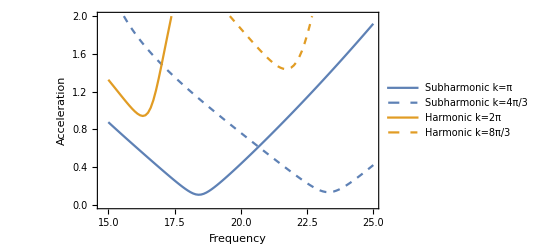

boundaries.pdf

```mathematica
p=ListPlot[{Transpose[{freqs/(2*Pi),Re[(Transpose[SortBy[#,Re[#]&]&/@subharmonic])[[6]]]/980}],Transpose[{freqs/(2*Pi),Re[(Transpose[SortBy[#,Re[#]&]&/@subharmonic2])[[6]]]/980}],Transpose[{freqs/(2*Pi),Re[(Transpose[SortBy[#,Re[#]&]&/@harmonic])[[7]]]/980}],Transpose[{freqs/(2*Pi),Re[(Transpose[SortBy[#,Re[#]&]&/@harmonic2])[[7]]]/980}]},PlotRange->{0,2},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[2]],Dashed]},PlotLegends->{"Subharmonic k=π","Subharmonic k=4π/3","Harmonic k=2π","Harmonic k=8π/3"}]
Export["boundaries.pdf",p]
```

### periodic

```mathematica
C1[m1_,m2_,n1_,n2_]:=ⅇ^(- h0 κ1[n1,m1])*BesselI[n1-n2,1/2 as κ1[n1,m1]]*BesselI[m1-m2,1/2 as κ1[n1,m1]]+ⅇ^(h0 κ1[n1,m1])*BesselI[n1-n2,-1/2 as κ1[n1,m1]]*BesselI[m1-m2,-1/2 as κ1[n1,m1]]
S1[m1_,m2_,n1_,n2_]:=ⅇ^(-h0 κ1[n1,m1])*BesselI[n1-n2,1/2 as κ1[n1,m1]]*BesselI[m1-m2,1/2 as κ1[n1,m1]]-ⅇ^(h0 κ1[n1,m1])*BesselI[n1-n2,-1/2 as κ1[n1,m1]]*BesselI[m1-m2,-1/2 as κ1[n1,m1]]
C2[l1_,m1_,m2_,n1_,n2_]:=ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,1/2 as Ω1[n1,m1,l1]]*BesselI[m1-m2,1/2 as Ω1[n1,m1,l1]]+ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,-1/2 as Ω1[n1,m1,l1]]*BesselI[m1-m2,-1/2 as Ω1[n1,m1,l1]]
S2[l1_,m1_,m2_,n1_,n2_]:=ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,1/2 as Ω1[n1,m1,l1]]*BesselI[m1-m2,1/2 as Ω1[n1,m1,l1]]-ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,-1/2 as Ω1[n1,m1,l1]]*BesselI[m1-m2,-1/2 as Ω1[n1,m1,l1]]
κx[n1_,m1_]:=qx+n1*q1.{1,0}+m1*q2.{1,0}
κy[n1_,m1_]:=qy+n1*q1.{0,1}+m1*q2.{0,1}
κ1[n1_,m1_]:=(κx[n1,m1]^2+κy[n1,m1]^2)^(1/2)
Ω1[n1_,m1_,l1_]:=(I*ρ/μ*(ω+l1*ωd)+κ1[n1,m1]^2)^(1/2)
mat1[n1_,n2_,m1_,m2_,l1_,l2_]:={{C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κx[n1,m2]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-((ⅈ κx[n1,m1] (C1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1]))+(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) (2 μ √(ρ/μ) (C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2]) κ1[n1,m1] √Ω1[n1,m1,l1]+S1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))))/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1])))},{-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κy[n1,m1]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-((ⅈ κy[n1,m1] (C1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1]))+(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) (2 μ √(ρ/μ) (C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2]) κ1[n1,m1] √Ω1[n1,m1,l1]+S1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))))/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1])))},{ⅈ μ κx[n1,m1] (S2[l1,m1,m2,n1,n2]/(μ √((ρ Ω1[n1,m1,l1])/μ))-(2 S1[m1,m2,n1,n2] κ1[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])),ⅈ μ κy[n1,m1] (S2[l1,m1,m2,n1,n2]/(μ √((ρ Ω1[n1,m1,l1])/μ))-(2 S1[m1,m2,n1,n2] κ1[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])),1/2 (C1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])+κ1[n1,m1] (2 μ (-C2[l1,m1,m2,n1,n2]+S2[l1,m1,m2,n1,n2]) κ1[n1,m1]+(S1[m1,m2,n1,n2] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √((ρ Ω1[n1,m1,l1])/μ))))/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])))}} l1,l2
mat2[n1_,n2_,m1_,m2_,l1_,l2_]:={{0,0,-(ⅈ ρ^2 C1[m1,m2,n1,n2] κ1[n1,m1] κx[n1,m1])/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1]))},{0,0,-(ⅈ ρ^2 C1[m1,m2,n1,n2] κ1[n1,m1] κy[n1,m1])/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1]))},{0,0,(ρ^2 S1[m1,m2,n1,n2] κ1[n1,m1])/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))}} (-1/2 (-1+l1,l2+1+l1,l2))
```

```mathematica
ks=(2*Pi/1.);
q1=ks*{1,-1/3.^(1/2)};
q2=ks*{0,2/3.^(1/2)};
qx=2*Pi/2;
qy=0;
freq=2*((qx^2+qy^2)^(1/2)*Tanh[h0*(qx^2+qy^2)^(1/2)]*(g+σ*(qx^2+qy^2)))^(1/2);
freq=2*Pi*18.;
g=980;
σ=20;
μ=0.05;
ρ=1;
h0=0.5;
ωd=freq;
ω=0.5*freq;
as=0.01;
```

```mathematica
M=3;
M2=3;

Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[mat1[n1,n2,m1,m2,l1,l2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[mat2[n1,n2,m1,m2,l1,l2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{558.537,Null}

{69.1639,Null}

```mathematica
rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];

ws={};
vs={};
λs={};
w=lev[[All,-1]];
v=rev[[All,-1]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].eq1.v/(Conjugate[w].eq2.v);
Print[k, " ", λ," ", Norm[eq1.v-λ*eq2.v]," ", Norm[Conjugate[Transpose[eq1]].w-Conjugate[λ*Transpose[eq2]].w]];
v=Quiet[LinearSolve[(λ*eq2-eq1),eq2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*eq2-eq1)]],Conjugate[Transpose[eq2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
```

1 -1.17257×10^7+0.0000889441 ⅈ 1.36522×10^6 1.82073×10^6

2 -2651.35+362.773 ⅈ 9043.18 238.023

3 -3197.16+726.404 ⅈ 46.3604 40.917

4 -3116.59+649.307 ⅈ 2.33777 1.55824

5 -3115.89+649.428 ⅈ 0.00352251 0.000775812

6 -3115.89+649.428 ⅈ 8.01497×10^-8 1.53523×10^-7

7 -3115.89+649.428 ⅈ 6.22715×10^-8 6.42743×10^-8

8 -3115.89+649.428 ⅈ 5.28042×10^-8 4.90324×10^-8

9 -3115.89+649.428 ⅈ 6.16886×10^-8 9.66628×10^-8

10 -3115.89+649.428 ⅈ 7.92808×10^-8 4.20068×10^-8

{11.8812,Null}

```mathematica
AbsoluteTiming[{evalsfull,evecsfull}=Eigensystem[{eq1,eq2}];]
SortBy[evalsfull,Abs[Im[#]]&]
```

{19.787,Null}

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-24553.4+0.946287 ⅈ,24541.4-0.952678 ⅈ,24599.9-0.962815 ⅈ,-24594.7+0.963118 ⅈ,11540.3-1.61036 ⅈ,11540.3-1.61036 ⅈ,-11540.3+1.61038 ⅈ,-11540.3+1.61043 ⅈ,-5998.2+2.73239 ⅈ,5998.2-2.73243 ⅈ,-5998.2+2.73246 ⅈ,5998.2-2.73246 ⅈ,-5998.2+2.73248 ⅈ,-5998.2+2.73248 ⅈ,5998.2-2.73249 ⅈ,5998.19-2.7325 ⅈ,42749.8-3.47822 ⅈ,-42749.8+3.47822 ⅈ,-42749.8+3.47822 ⅈ,42749.8-3.47822 ⅈ,42749.8-3.47822 ⅈ,-42749.8+3.47822 ⅈ,-45605.8-12.0585 ⅈ,-45605.8-12.0585 ⅈ,45605.8+12.0585 ⅈ,45605.8+12.0585 ⅈ,45605.8+12.0585 ⅈ,-45605.8-12.0585 ⅈ,51307.7+37.0078 ⅈ,-51307.7-37.0078 ⅈ,-51307.7-37.0078 ⅈ,51307.7+37.0078 ⅈ,-51307.7-37.0078 ⅈ,51307.7+37.0078 ⅈ,-41555.7+40.3661 ⅈ,41555.7-40.3711 ⅈ,41555.7-40.3896 ⅈ,-41555.7+40.3915 ⅈ,-91521.8+55.3814 ⅈ,-91713.6+56.1448 ⅈ,91505.-57.9882 ⅈ,91698.1-59.2816 ⅈ,34214.6-62.9004 ⅈ,-34214.6+62.9004 ⅈ,-34214.6+62.9004 ⅈ,34214.6-62.9004 ⅈ,-34214.6+62.9004 ⅈ,34214.6-62.9004 ⅈ,-34214.6+62.9004 ⅈ,34214.6-62.9004 ⅈ,59812.8+63.3148 ⅈ,-59812.8-63.3148 ⅈ,76640.2+95.1374 ⅈ,-76640.2-95.1374 ⅈ,-76640.2-95.1374 ⅈ,76640.2+95.1374 ⅈ,79424.6+98.9899 ⅈ,-79424.6-98.9899 ⅈ,79424.6+98.9899 ⅈ,-79424.6-98.9899 ⅈ,28623.4-105.11 ⅈ,-28623.4+105.11 ⅈ,-28623.4+105.11 ⅈ,28623.4-105.11 ⅈ,-84979.4-105.947 ⅈ,84979.4+105.947 ⅈ,25870.6-122.739 ⅈ,-25870.6+122.739 ⅈ,-25870.6+122.739 ⅈ,25870.6-122.739 ⅈ,-33503.5-128.021 ⅈ,-33503.5-128.021 ⅈ,-33503.5-128.021 ⅈ,33503.5+128.021 ⅈ,33503.5+128.021 ⅈ,33503.5+128.021 ⅈ,-33503.5-128.021 ⅈ,33503.5+128.021 ⅈ,-44896.6-130.716 ⅈ,44896.6+130.716 ⅈ,44896.6+130.716 ⅈ,-44896.6-130.716 ⅈ,50511.6+135.81 ⅈ,-50511.6-135.81 ⅈ,50511.6+135.81 ⅈ,-50511.6-135.81 ⅈ,-118019.-135.878 ⅈ,-118019.-135.878 ⅈ,118019.+135.878 ⅈ,118019.+135.878 ⅈ,-120756.-137.839 ⅈ,120756.+137.839 ⅈ,27732.1+139.692 ⅈ,-27732.1-139.692 ⅈ,27732.1+139.692 ⅈ,27732.1+139.692 ⅈ,-27732.1-139.692 ⅈ,27732.1+139.692 ⅈ,-27732.1-139.692 ⅈ,-27732.1-139.692 ⅈ,61586.5+147.14 ⅈ,-61586.5-147.14 ⅈ,61586.5+147.14 ⅈ,61586.5+147.14 ⅈ,-61586.5-147.14 ⅈ,-61586.5-147.14 ⅈ,-61586.5-147.14 ⅈ,61586.5+147.14 ⅈ,94323.7+148.303 ⅈ,-94323.7-148.303 ⅈ,-92244.6-148.536 ⅈ,92244.6+148.536 ⅈ,92244.6+148.536 ⅈ,-92244.6-148.536 ⅈ,-129536.-149.882 ⅈ,129536.+149.882 ⅈ,-20372.9+153.253 ⅈ,20372.9-153.253 ⅈ,-20372.9+153.253 ⅈ,-20372.9+153.253 ⅈ,20372.9-153.253 ⅈ,20372.9-153.253 ⅈ,-20372.9+153.253 ⅈ,20372.9-153.253 ⅈ,-67155.1-159.098 ⅈ,67155.1+159.098 ⅈ,77875.2+163.356 ⅈ,-77875.2-163.356 ⅈ,77875.2+163.356 ⅈ,-77875.2-163.356 ⅈ,-77875.2-163.356 ⅈ,77875.2+163.356 ⅈ,-62932.4-163.448 ⅈ,-62932.4-163.448 ⅈ,62932.4+163.448 ⅈ,62932.4+163.448 ⅈ,-167059.-165.347 ⅈ,167059.+165.347 ⅈ,60813.8+166.138 ⅈ,60813.8+166.138 ⅈ,-60813.8-166.138 ⅈ,-60813.8-166.138 ⅈ,-83235.5-168.363 ⅈ,83235.5+168.363 ⅈ,-83235.5-168.363 ⅈ,-83235.5-168.363 ⅈ,83235.5+168.363 ⅈ,83235.5+168.363 ⅈ,17521.5-175.069 ⅈ,-17521.5+175.069 ⅈ,17521.5-175.069 ⅈ,-17521.5+175.069 ⅈ,17521.5-175.069 ⅈ,17521.5-175.069 ⅈ,-17521.5+175.069 ⅈ,-17521.5+175.069 ⅈ,93873.4+177.813 ⅈ,93873.4+177.813 ⅈ,-93873.4-177.813 ⅈ,93873.4+177.813 ⅈ,-93873.4-177.813 ⅈ,-93873.4-177.813 ⅈ,109662.+190.78 ⅈ,-109662.-190.78 ⅈ,-47938.1-194.478 ⅈ,47938.1+194.478 ⅈ,-140815.-213.459 ⅈ,140815.+213.459 ⅈ,-140815.-213.459 ⅈ,140815.+213.459 ⅈ,-145967.-216.911 ⅈ,-145967.-216.911 ⅈ,145967.+216.911 ⅈ,145967.+216.911 ⅈ,41307.8+223.458 ⅈ,-41307.8-223.458 ⅈ,41307.8+223.458 ⅈ,41307.8+223.458 ⅈ,-41307.8-223.458 ⅈ,-41307.8-223.458 ⅈ,-156243.-223.585 ⅈ,156243.+223.585 ⅈ,-36738.-253.725 ⅈ,36738.+253.725 ⅈ,36738.+253.725 ⅈ,-36738.-253.725 ⅈ,36738.+253.725 ⅈ,-36738.-253.725 ⅈ,-217353.-258.672 ⅈ,217353.+258.672 ⅈ,-217353.-258.672 ⅈ,217353.+258.672 ⅈ,-222415.-261.294 ⅈ,222415.+261.294 ⅈ,34379.5+273.685 ⅈ,-34379.5-273.685 ⅈ,-34379.5-273.685 ⅈ,34379.5+273.685 ⅈ,34379.5+273.685 ⅈ,-34379.5-273.685 ⅈ,308045.+300.974 ⅈ,-308045.-300.974 ⅈ,-26761.5-360.211 ⅈ,-26761.5-360.211 ⅈ,26761.5+360.211 ⅈ,26761.5+360.211 ⅈ,26761.5+360.211 ⅈ,26761.5+360.211 ⅈ,-26761.5-360.211 ⅈ,-26761.5-360.211 ⅈ,-20796.3-448.47 ⅈ,-20796.3-448.47 ⅈ,20796.3+448.47 ⅈ,20796.3+448.47 ⅈ,-17271.9-514.193 ⅈ,17271.9+514.193 ⅈ,-17271.9-514.193 ⅈ,17271.9+514.193 ⅈ,-4302.31+785.95 ⅈ,4302.31-785.95 ⅈ,-4302.31+785.95 ⅈ,4302.31-785.95 ⅈ,4302.29-785.959 ⅈ,-4302.29+785.959 ⅈ,-4302.29+785.959 ⅈ,4302.29-785.959 ⅈ,-7024.04-1051.36 ⅈ,7024.04+1051.36 ⅈ,-7024.04-1051.36 ⅈ,7024.04+1051.36 ⅈ,7024.04+1051.36 ⅈ,-7024.04-1051.36 ⅈ,-7024.04-1051.36 ⅈ,7024.04+1051.36 ⅈ,7071.9+1136.27 ⅈ,-7071.9-1136.27 ⅈ,-7071.9-1136.27 ⅈ,7071.9+1136.27 ⅈ,-7071.86-1136.29 ⅈ,7071.86+1136.29 ⅈ,-7071.87-1136.29 ⅈ,7071.86+1136.29 ⅈ,5671.69-4928.59 ⅈ,-5671.69+4928.6 ⅈ,-5671.69+4928.6 ⅈ,5671.69-4928.6 ⅈ,-5671.75-4928.75 ⅈ,-5671.75-4928.75 ⅈ,5671.75+4928.75 ⅈ,5671.75+4928.76 ⅈ,785.826+8068.81 ⅈ,-785.826-8068.81 ⅈ,-785.826-8068.81 ⅈ,785.826+8068.81 ⅈ,785.826+8068.81 ⅈ,-785.826-8068.81 ⅈ,785.826+8068.81 ⅈ,-785.826-8068.81 ⅈ,-6171.27-8984.87 ⅈ,-6171.27-8984.87 ⅈ,6171.27+8984.87 ⅈ,6171.27+8984.87 ⅈ,6171.27+8984.87 ⅈ,6171.27+8984.87 ⅈ,-6171.27-8984.88 ⅈ,-6171.27-8984.88 ⅈ,-6156.53+8990.04 ⅈ,6156.54-8990.04 ⅈ,6156.54-8990.04 ⅈ,-6156.54+8990.04 ⅈ,-6156.54+8990.04 ⅈ,-6156.54+8990.04 ⅈ,6156.54-8990.04 ⅈ,6156.54-8990.04 ⅈ,-3546.11+12707.1 ⅈ,-3546.11+12707.1 ⅈ,3546.11-12707.1 ⅈ,3546.11-12707.1 ⅈ,3608.+12899.9 ⅈ,-3608.-12899.9 ⅈ,3608.+12899.9 ⅈ,-3608.-12899.9 ⅈ,18.2362-17354.4 ⅈ,-18.2362+17354.4 ⅈ,-18.2361+17354.4 ⅈ,18.2362-17354.4 ⅈ,18.2371-17354.4 ⅈ,-18.237+17354.4 ⅈ,-18.2369+17354.4 ⅈ,18.2371-17354.4 ⅈ,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity}